1

0.5

{6.90559,3.35604,2.4814,2.00614,1.6969,1.47606,1.30877,1.1767,1.0692,0.979614,0.903554,0.83799,0.780761,0.73028,0.685352,0.645058,0.60868,0.575644,0.54549,0.517839,0.492383,0.468859,0.447051,0.426773,0.407866,0.390194,0.373639,0.358098,0.343481,0.329709,0.316711,0.304425,0.292797,0.281775,0.271315,0.261378,0.251927,0.242929,0.234354,0.226174,0.218366,0.210905,0.203771,0.196945,0.190409,0.184147,0.178142,0.172383,0.166854,0.161544,0.156443,0.151538,0.146821,0.142282,0.137913,0.133705,0.129651,0.125745,0.121978,0.118345}

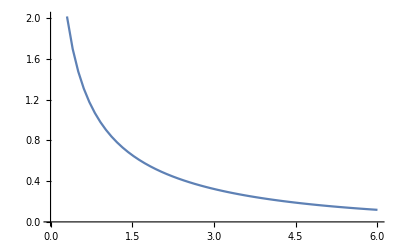

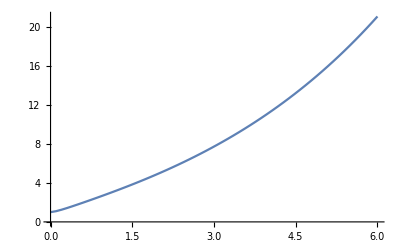

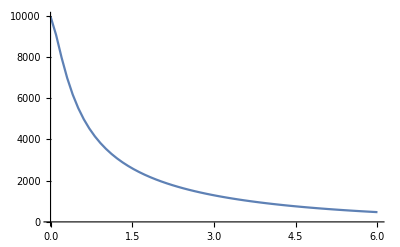

```mathematica
A=1
J=0.5
J001=Table[u/.FindRoot[A×x^-1.5×ⅇ^(-J×x)×∑_(l=1)^10000 l^1.5×ⅇ^(-u×l)-1,{u,0.01}],{x,0.01,6,0.1}]
ListLinePlot[J001,DataRange->{0,6}]
ListLinePlot[{(∑_(l=1)^10000 l^2.5×ⅇ^(-J001×l))/(∑_(l=1)^10000 l^1.5×ⅇ^(-J001×l))},DataRange->{0,6}]
ListLinePlot[{(∑_(l=1)^10000 l^1.5×ⅇ^(-J001×l))/(∑_(l=1)^10000 l^2.5×ⅇ^(-J001×l))×10000},DataRange->{0,6}]
```

```mathematica
avg1 = (∑_(l=1)^10000 l^2.5×ⅇ^(-J001×l))/(∑_(l=1)^10000 l^1.5×ⅇ^(-J001×l))
```

{1.00284,1.10166,1.25488,1.43084,1.61769,1.81043,2.00691,2.20626,2.40821,2.61279,2.82013,3.03044,3.24397,3.46096,3.68166,3.90631,4.13516,4.36844,4.60637,4.84918,5.0971,5.35032,5.60907,5.87357,6.14401,6.42061,6.70357,6.99311,7.28944,7.59277,7.90331,8.22127,8.54688,8.88036,9.22192,9.5718,9.93022,10.2974,10.6736,11.0591,11.454,11.8587,12.2735,12.6984,13.1339,13.5802,14.0376,14.5063,14.9867,15.479,15.9835,16.5005,17.0304,17.5735,18.13,18.7003,19.2848,19.8838,20.4977,21.1268}

{690.559,30.5095,11.8162,6.47143,4.13879,2.89424,2.14552,1.65732,1.32,1.0765,0.894608,0.754946,0.645257,0.557465,0.486065,0.427191,0.378062,0.336634,0.301375,0.27112,0.244966,0.222208,0.202286,0.18475,0.169239,0.155456,0.143157,0.13214,0.122235,0.113302,0.10522,0.097886,0.0912139,0.0851283,0.0795647,0.0744668,0.0697859,0.0654795,0.0615102,0.0578451,0.0544553,0.0513151,0.0484017,0.0456949,0.0431767,0.0408307,0.0386426,0.0365993,0.034689,0.0329011,0.0312261,0.0296552,0.0281806,0.0267951,0.0254922,0.0242659,0.0231108,0.0220218,0.0209944,0.0200245}

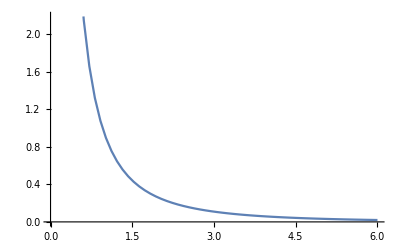

{0.01,0.11,0.21,0.31,0.41,0.51,0.61,0.71,0.81,0.91,1.01,1.11,1.21,1.31,1.41,1.51,1.61,1.71,1.81,1.91,2.01,2.11,2.21,2.31,2.41,2.51,2.61,2.71,2.81,2.91,3.01,3.11,3.21,3.31,3.41,3.51,3.61,3.71,3.81,3.91,4.01,4.11,4.21,4.31,4.41,4.51,4.61,4.71,4.81,4.91,5.01,5.11,5.21,5.31,5.41,5.51,5.61,5.71,5.81,5.91}

-Graphics-

-Graphics-

```mathematica
anotherJ001=Table[u/.FindRoot[A*x^-1.5*ⅇ^(-J*x)*∑_(l=1)^10000 l^1.5*ⅇ^(-u*x*l)-1,{u,0.01}],{x,0.01,6,0.1}]
ListLinePlot[anotherJ001,DataRange->{0,6}]
x= Range[0.01,6,0.1]

ListLinePlot[{(∑_(l=1)^10000 l^2.5*ⅇ^(-anotherJ001*x*l))/(∑_(l=1)^10000 l^1.5*ⅇ^(-anotherJ001*x*l))},DataRange->{0,6}]
ListLinePlot[{(∑_(l=1)^10000 l^1.5*ⅇ^(-anotherJ001*x*l))/(∑_(l=1)^10000 l^2.5*ⅇ^(-anotherJ001*x*l))×10000},DataRange->{0,6}]
```

```mathematica
avg2 = (∑_(l=1)^10000 l^2.5*ⅇ^(-anotherJ001*x*l))/(∑_(l=1)^10000 l^1.5*ⅇ^(-anotherJ001*x*l))
```

{1.00284,1.10166,1.25488,1.43084,1.61769,1.81043,2.00691,2.20626,2.40821,2.61279,2.82013,3.03044,3.24397,3.46096,3.68166,3.90631,4.13516,4.36844,4.60637,4.84918,5.0971,5.35032,5.60907,5.87357,6.14401,6.42061,6.70357,6.99311,7.28944,7.59277,7.90331,8.22127,8.54688,8.88036,9.22192,9.5718,9.93022,10.2974,10.6736,11.0591,11.454,11.8587,12.2735,12.6984,13.1339,13.5802,14.0376,14.5063,14.9867,15.479,15.9835,16.5005,17.0304,17.5735,18.13,18.7003,19.2848,19.8838,20.4977,21.1268}

```mathematica
avg1- avg2
```

{0.,0.,-2.22045×10^-16,6.66134×10^-16,-6.66134×10^-16,0.,4.44089×10^-16,-8.88178×10^-16,-4.44089×10^-16,-4.44089×10^-16,-4.44089×10^-16,4.44089×10^-16,-8.88178×10^-16,0.,0.,-8.88178×10^-16,7.10543×10^-15,0.,-8.88178×10^-16,-8.88178×10^-16,1.77636×10^-15,-7.99361×10^-15,3.37508×10^-14,8.88178×10^-16,1.77636×10^-15,-6.21725×10^-15,0.,0.,0.,-1.15463×10^-14,3.19744×10^-14,1.77636×10^-15,0.,-2.27374×10^-13,0.,0.,-1.77636×10^-15,-1.77636×10^-15,-5.25802×10^-13,3.55271×10^-14,1.77636×10^-15,0.,-3.55271×10^-15,1.77636×10^-15,-1.72307×10^-13,0.,-1.77636×10^-15,3.55271×10^-15,1.77636×10^-15,4.79616×10^-14,-3.19744×10^-13,-1.42109×10^-14,-3.55271×10^-15,3.55271×10^-15,1.06581×10^-14,0.,-1.247×10^-12,-4.26326×10^-14,-3.55271×10^-15,3.83693×10^-13}

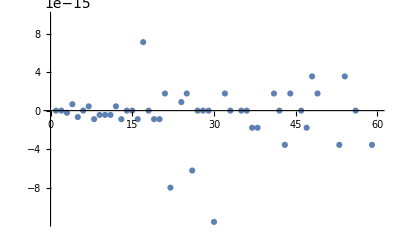

```mathematica
ListPlot[%38]
```